# Упражнение 2

```mathematica
logisticIC=0.01;
logisticExact[t_]:=0.01/(0.01+0.99E^(-10t))
errorListPlot[approx_]:=(
ListPlot[Table[{approx[[i,1]],Abs[logisticExact[approx[[i,1]]]-approx[[i,2]]]},{i,1,Length[approx]}]]
);
```

## Explicit Euler

```mathematica
explicitEuler[ic_,Δt_,T_]:=(
Block[{sol,n,i},
n=T/Δt;
sol=Table[0,{n+1}];
sol[[1]]=ic;
For[i=1,i≤n,++i,
sol[[i+1]]=sol[[i]]+Δt*10sol[[i]](1-sol[[i]]);
];
{sol,Table[{(i-1)Δt,sol[[i]]},{i,1,Length[sol]}]}
]
);
```

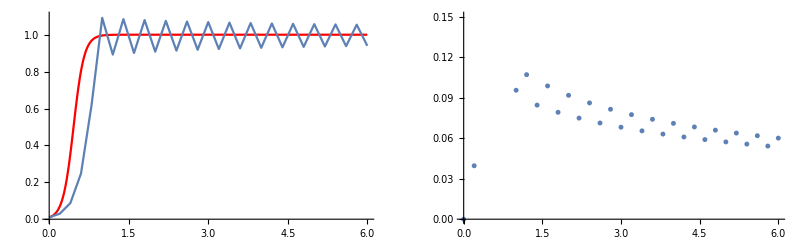

```mathematica
(*
Явен метод на Ойлер приложен за логистичното уравнение
Както е показано на лекции за h=0.2 методът е А-устойчив, но не схожда
За h < 0.2 методът схожда, но решението осцилира около точното
За h < 0.1 методът е монотонен
За h > 0.2 методът има лошо поведение и не схожда
Най-често условието за монотонност е по-силно от това за А-устойчивост, което означава, че щом методът е монотонен той е и А-устойчив
*)
explicitNodes1 = explicitEuler[logisticIC,0.2,6];
GraphicsRow[{Show[
Plot[logisticExact[t],{t,0,6},PlotRange->{{0,6},{0,1.1}},PlotStyle->Red],
ListLinePlot[explicitNodes1[[2]],PlotRange->{{0,6},{0,1.1}}]
],
errorListPlot[explicitNodes1[[2]]]
}
]
```

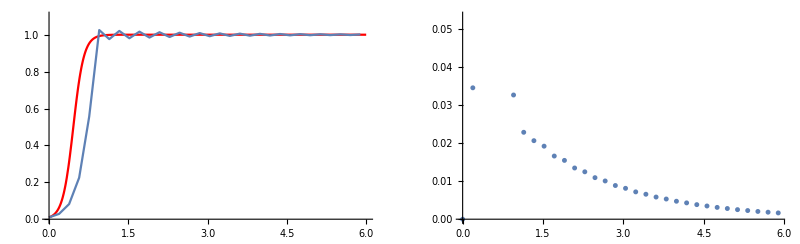

```mathematica
explicitNodes2 = explicitEuler[logisticIC,0.19,6];
GraphicsRow[{Show[
Plot[logisticExact[t],{t,0,6},PlotRange->{{0,6},{0,1.1}},PlotStyle->Red],
ListLinePlot[explicitNodes2[[2]],PlotRange->{{0,6},{0,1.1}}]
],
errorListPlot[explicitNodes2[[2]]]
}
]
```

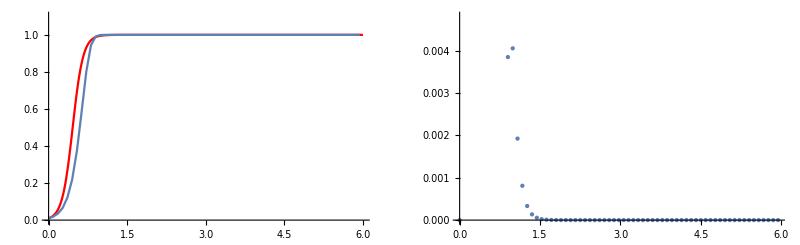

```mathematica
explicitNodes3 = explicitEuler[logisticIC,0.09,6];
GraphicsRow[{Show[
Plot[logisticExact[t],{t,0,6},PlotRange->{{0,6},{0,1.1}},PlotStyle->Red],
ListLinePlot[explicitNodes3[[2]],PlotRange->{{0,6},{0,1.1}}]
],
errorListPlot[explicitNodes3[[2]]]
}
]
```

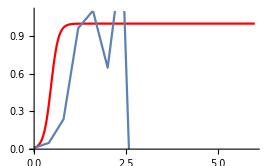

```mathematica
explicitNodes4 = explicitEuler[logisticIC,0.4,6];
GraphicsRow[{Show[
Plot[logisticExact[t],{t,0,6},PlotRange->{{0,6},{0,1.1}},PlotStyle->Red],
ListLinePlot[explicitNodes4[[2]],PlotRange->{{0,6},{0,1.1}}]
],
errorListPlot[explicitNodes4[[2]]]
}
]
```

## Implicit Euler

```mathematica
implicitEuler[ic_,Δt_,T_]:=(
Block[{sol,n,i,yNew,yNewIC},
n=T/Δt;
sol=Table[0,{n+1}];
sol[[1]]=ic;
For[i=1,i≤n,++i,
(*
Нелинейното уравнение може да се реши по-два начина чрез FindRoot и NSolve
В случая уравнението има точно решение и NSolve може да се справи със задачата,
в общия случай обаче или уравнението няма явно решение или нямаме явна форма за него
и се налага да използваме числен метод. FindRoot е функция за приближено решаване на уравнения,
която използва числен метод. За уравнението тук може да се покаже, че има 2 решения:
положително и отрицателно, може също да се покаже, че на нас ни трябва положителното.
*)
(*
Решение чрез FindRoot
yNewIC=sol[[i]]+Δt*10sol[[i]](1-sol[[i]]);
sol[[i+1]]=yNew/.FindRoot[yNew==sol[[i]]+10Δt*yNew(1-yNew),{yNew,yNewIC}];
*)
(*Решение чрез NSolve*)
sol[[i+1]]=yNew/.NSolve[yNew==sol[[i]]+10Δt*yNew(1-yNew)&&yNew>0,yNew][[1]];
];
{sol,Table[{(i-1)Δt,sol[[i]]},{i,1,Length[sol]}]}
]
);
```

```mathematica
(*
Както е показано на лекции неявният метод на Ойлер е безусловно А-устойчив и безусловно монотонен.
*)
```

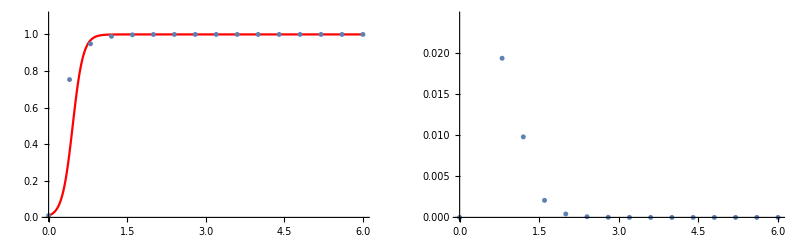

```mathematica
implicit4Nodes = implicitEuler[logisticIC,0.4,6];
GraphicsRow[{Show[
Plot[logisticExact[t],{t,0,6},PlotRange->{{0,6},{0,1.1}},PlotStyle->Red],
ListPlot[implicit4Nodes[[2]],PlotRange->{{0,6},{0,2}}]
],
errorListPlot[implicit4Nodes[[2]]]
}
]
```